## Functions

```mathematica
makeLine[x_, y_, L_, theta_]:={{x, y}, {x+L*Cos[theta], y+L*Sin[theta]}}
```

```mathematica
getSlope[{{xa1_, ya1_}, {xa2_, ya2_}}]:=If[xa2-xa1== 0, "undefined",(ya2-ya1)/(xa2-xa1)]
```

```mathematica
getYintercept[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{m},
m=getSlope[ {{xa1, ya1}, {xa2, ya2}}];
 If[m=="undefined", "undefined", ya1-m*xa1] ]
```

```mathematica
intersectPoint[{{xa1_, ya1_}, {xa2_, ya2_}},  {{xb1_, yb1_}, {xb2_, yb2_}}]:=Module[{mA, mB, bA, bB, yI, xI},
mA=getSlope[{{xa1, ya1}, {xa2, ya2}}];
mB=getSlope[{{xb1, yb1}, {xb2, yb2}}];
bA=getYintercept[{{xa1, ya1}, {xa2, ya2}}];
bB=getYintercept[{{xb1, yb1}, {xb2, yb2}}];
If[mA==mB, {-999, -999},
If[mA=="undefined", If[mB==0, {xa1, yb1}, {xa1, mB*xa1+bB}], 
If[mB=="undefined",If[mA==0, {xb1, ya1},  {xb1, mA*xb1*bA}],
 {(bB-bA)/(mA-mB), mA*(bB-bA)/(mA-mB)+bA}]]]]
```

```mathematica
pointInDomainQ[{{xa1_, ya1_}, {xa2_, ya2_}}, {xb_, yb_}]:=If[((xa1≤ xb ≤ xa2) && (ya1≤ yb ≤ya2)) || 
((xa1>= xb >= xa2) && (ya1<= yb <=ya2)) ||
((xa1>= xb >= xa2) && (ya1>= yb >=ya2)) ||
((xa1<= xb <= xa2) && (ya1>= yb >=ya2))
, True, False]
```

```mathematica
linesIntersectQ[line1_, line2_]:=Module[{point},
point=intersectPoint[line1, line2];
If[{pointInDomainQ[line1, point], pointInDomainQ[line2, point]}=={True, True}, True, False]]
```

```mathematica
makeSquareOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}]:=Module[{L, theta},
L=Sqrt[(xa2-xa1)^2+(ya2-ya1)^2];
theta=ArcTan[(ya2-ya1)/(xa2-xa1)];
{{xa1, ya1}, {xa2, ya2}, {xa2+L*Sin[theta], ya2-L*Cos[theta]}, {xa1+L*Sin[theta], ya1-L*Cos[theta]}}]
```

```mathematica
makeRectangleOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}, L_]:=Module[{ theta},
(* Need to account for time when xa1=xa2 *)
theta=If[xa2==xa1, Pi/2, ArcTan[(ya2-ya1)/(xa2-xa1)]];
{{xa1, ya1}, {xa2, ya2}, {xa2+L*Sin[theta], ya2-L*Cos[theta]}, {xa1+L*Sin[theta], ya1-L*Cos[theta]}}]
```

```mathematica
generateLinesFromPolygon[polygon_]:=Module[{length},
length=Length[polygon];
Append[{polygon[[#]], polygon[[#+1]]}&/@Range[length-1],{ polygon[[length]], polygon[[1]]}]]
```

```mathematica
isPointInPolygon[polygon_, {x_, y_}]:=OddQ[Length[Select[Flatten[linesIntersectQ[#, {{x, y}, {-100, y}}]&/@generateLinesFromPolygon[polygon]],#== True &]]]
```

```mathematica
polygonIntersectQ[polygon1_, polygon2_]:=Module[{lines1, lines2, linesIntersect, cornersInside},
lines1=generateLinesFromPolygon[polygon1];
lines2=generateLinesFromPolygon[polygon2];
linesIntersect=If[MemberQ[Complement[Flatten[Table[Table[{linesIntersectQ[lines2[[j]], lines1[[i]]],linesIntersectQ[lines1[[i]], lines2[[j]]]}, {i, 1, Length[polygon1]}], {j, 1, Length[polygon2]}]]], True], True, False];
cornersInside=MemberQ[Flatten[{isPointInPolygon[polygon1, #]&/@polygon2, isPointInPolygon[polygon2, #]&/@polygon1}], True];
MemberQ[Flatten[{linesIntersect, cornersInside}], True]]
```

```mathematica
polyBoundA={{-1, 0}, {11, 0}, {11, -1}, {-1, -1}};
polyBoundB={{0, -1}, {0, 11}, {-1, 11}, {-1, -1}};
polyBoundC={{-1, 10}, {11, 10}, {11, 11}, {-1, 11}};
polyBoundD={{10, -1}, {10, 11}, {11, 11}, {11, -1}};
boundingPoys={polyBoundA, polyBoundB, polyBoundC, polyBoundD};
```

```mathematica
computePieces[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,2*Pi*Random[]], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];];
rectList]
```

```mathematica
computePieces3[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,Pi*Round[3*Random[]]/2], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];
If[Mod[i,100]==0, Print[{i,Length[rectList]}]];];
rectList]
```

```mathematica
computePieces2[L_, W_, n_]:=Module[{ rectList, newSquare, interSectQ, i},
rectList={};
For[i=1, i<n, i++,
newSquare=makeRectangleOffLine[makeLine[10*Random[],  10*Random[], L,0], W];
interSectQ=Complement[Join[polygonIntersectQ[#, newSquare]&/@boundingPoys, polygonIntersectQ[#, newSquare]&/@rectList]];
rectList=If[interSectQ=={False}, Append[rectList, newSquare], rectList];
If[Mod[i,100]==0, Print[{i,Length[rectList]}]];];
rectList]
```

```mathematica
showResults[data_]:=Graphics[{ Black,(Line[#]&/@generateLinesFromPolygon[#])&/@data,Blue,(Line[#]&/@generateLinesFromPolygon[#])&/@boundingPoys}]
```

```mathematica
aa=computePieces[Sqrt[2], Sqrt[2], 200];
```

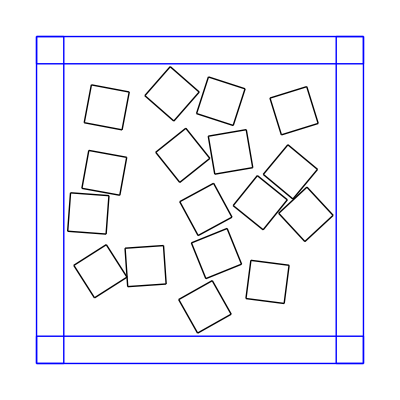

```mathematica
showResults[aa]
```

```mathematica
makeTriangleOffLine[{{xa1_, ya1_}, {xa2_, ya2_}}, L_]:=Module[{ theta},
(* Need to account for time when xa1=xa2 *)
theta=If[xa2==xa1, Pi/2, ArcTan[(ya2-ya1)/(xa2-xa1)]];
{{xa1, ya1}, {xa2, ya2}, {xa1+L*Cos[theta+Pi/3], ya1+L*Sin[theta+Pi/3]}}]
```

```mathematica
makeTriangle[x_, y_, L_, H_, theta_]:=(RotationMatrix[theta].#+{x,y})&/@{{0, 0}, {L, 0}, {L/2, H}}
```

```mathematica
makeTriagSet[nn_, L_]:=Module[{triList, newTri, interSectQ},
triList={};
For[i=1, i≤nn, i++,
newTri=makeTriangle[10*Random[], 10*Random[], L, 1/L, 2*Pi*Random[]];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];];
triList];
```

```mathematica
makeTriagSet2[nn_, L_]:=Module[{triList, newTri, interSectQ},
triList={};
For[i=1, i≤nn, i++,
newTri=makeTriangle[10*Random[], 10*Random[], L, 1/L, Pi*Round[3*Random[]]/2];
interSectQ=Complement[Join[polygonIntersectQ[#, newTri]&/@boundingPoys, polygonIntersectQ[#, newTri]&/@triList]];
triList=If[interSectQ=={False}, Append[triList, newTri], triList];];
triList]
```

```mathematica
showTriangle[L_]:=Graphics[{ Line[#]&/@generateLinesFromPolygon[makeTriangle[0, 0,L, 1/L, 0]]}]
```

```mathematica
bb=makeTriagSet2[200, 1];
```

1

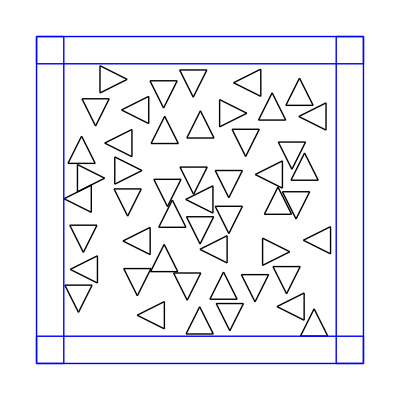

```mathematica
showResults[bb]
```